```mathematica
Chart
```

```mathematica
isotopes=EntityValue["Isotope",{EntityProperty["Isotope","AtomicNumber"],EntityProperty["Isotope","NeutronNumber"],EntityProperty["Isotope","AtomicSymbol"],EntityProperty["Isotope","BindingEnergy"]}];
```

```mathematica
isotopes[[;;10]]
```

{{1,0,H,0. MeV},{1,1,H,1.11228 MeV},{1,2,H,2.82727 MeV},{1,3,H,2. MeV},{1,4,H,1. MeV},{1,5,H,1. MeV},{1,6,H,0.9 MeV},{2,0,He,Missing[Unknown]},{2,1,He,2.57268 MeV},{2,2,He,7.073916 MeV}}

```mathematica
sel=Select[isotopes,0<=#[[1]]<=20∧0<#[[2]]<52&]
```

{{1,1,H,1.11228 MeV},{1,2,H,2.82727 MeV},{1,3,H,2. MeV},{1,4,H,1. MeV},{1,5,H,1. MeV},{1,6,H,0.9 MeV},{2,1,He,2.57268 MeV},{2,2,He,7.073916 MeV},{2,3,He,5.5 MeV},{2,4,He,4.8785 MeV},{2,5,He,4.12 MeV},{2,6,He,3.9245 MeV},{2,7,He,3.3 MeV},{2,8,He,3. MeV},{3,1,Li,1. MeV},{3,2,Li,5.3 MeV},{3,3,Li,5.33233 MeV},{3,4,Li,5.60644 MeV},{3,5,Li,5.1597 MeV},{3,6,Li,5.0378 MeV},{3,7,Li,4.53 MeV},{3,8,Li,4.155 MeV},{3,9,Li,3.8 MeV},{3,10,Li,3.5 MeV},{4,1,Be,0.018 MeV},{4,2,Be,4.49 MeV},{4,3,Be,5.3715 MeV},{4,4,Be,7.0624 MeV},{4,5,Be,6.4627 MeV},{4,6,Be,6.4976 MeV},{4,7,Be,5.9525 MeV},{4,8,Be,5.721 MeV},{4,9,Be,5.24 MeV},{4,10,Be,5. MeV},{4,11,Be,4.5 MeV},{4,12,Be,4.3 MeV},{5,1,B,-0.467 MeV},{5,2,B,3.6 MeV},{5,3,B,4.717 MeV},{5,4,B,6.257 MeV},{5,5,B,6.47508 MeV},{5,6,B,6.92773 MeV},{5,7,B,6.631 MeV},{5,8,B,6.496 MeV},{5,9,B,6.1 MeV},{5,10,B,5.88 MeV},{5,11,B,5.51 MeV},{5,12,B,5.3 MeV},{5,13,B,5. MeV},{5,14,B,5. MeV},{5,15,B,4. MeV},{5,16,B,4. MeV},{6,2,C,3.1 MeV},{6,3,C,4.34 MeV},{6,4,C,6.032 MeV},{6,5,C,6.6765 MeV},{6,6,C,7.680145 MeV},{6,7,C,7.46985 MeV},{6,8,C,7.52032 MeV},{6,9,C,7.1 MeV},{6,10,C,6.922 MeV},{6,11,C,6.56 MeV},{6,12,C,6.43 MeV},{6,13,C,6.1 MeV},{6,14,C,6. MeV},{6,15,C,5.7 MeV},{6,16,C,5.4 MeV},{6,17,C,5. MeV},{7,3,N,4. MeV},{7,4,N,5.36 MeV},{7,5,N,6.17 MeV},{7,6,N,7.2389 MeV},{7,7,N,7.475615 MeV},{7,8,N,7.69946 MeV},{7,9,N,7.374 MeV},{7,10,N,7.29 MeV},{7,11,N,7.04 MeV},{7,12,N,6.95 MeV},{7,13,N,6.7 MeV},{7,14,N,6.6 MeV},{7,15,N,6.4 MeV},{7,16,N,6.2 MeV},{7,17,N,5.9 MeV},{7,18,N,5.6 MeV},{8,3,O,3.2 MeV},{8,4,O,4.88 MeV},{8,5,O,5.81 MeV},{8,6,O,7.05228 MeV},{8,7,O,7.4637 MeV},{8,8,O,7.976207 MeV},{8,9,O,7.750729 MeV},{8,10,O,7.767098 MeV},{8,11,O,7.566 MeV},{8,12,O,7.569 MeV},{8,13,O,7.39 MeV},{8,14,O,7.36 MeV},{8,15,O,7.2 MeV},{8,16,O,7. MeV},{8,17,O,6.7 MeV},{8,18,O,6.5 MeV},{8,19,O,6.2 MeV},{8,20,O,6. MeV},{9,4,F,4. MeV},{9,5,F,5.3 MeV},{9,6,F,6.5 MeV},{9,7,F,6.964 MeV},{9,8,F,7.5423 MeV},{9,9,F,7.6316 MeV},{9,10,F,7.779019 MeV},{9,11,F,7.72014 MeV},{9,12,F,7.738 MeV},{9,13,F,7.62 MeV},{9,14,F,7.62 MeV},{9,15,F,7.5 MeV},{9,16,F,7.3 MeV},{9,17,F,7.1 MeV},{9,18,F,6.9 MeV},{9,19,F,6.6 MeV},{9,20,F,6.4 MeV},{9,21,F,6.2 MeV},{9,22,F,6. MeV},{10,5,Ne,4.9 MeV},{10,6,Ne,6.08 MeV},{10,7,Ne,6.6405 MeV},{10,8,Ne,7.3413 MeV},{10,9,Ne,7.5673 MeV},{10,10,Ne,8.032241 MeV},{10,11,Ne,7.97171 MeV},{10,12,Ne,8.08047 MeV},{10,13,Ne,7.9553 MeV},{10,14,Ne,7.9933 MeV},{10,15,Ne,7.84 MeV},{10,16,Ne,7.75 MeV},{10,17,Ne,7.52 MeV},{10,18,Ne,7.4 MeV},{10,19,Ne,7.2 MeV},{10,20,Ne,7. MeV},{10,21,Ne,6.8 MeV},{10,22,Ne,6.7 MeV},{10,23,Ne,6.4 MeV},{10,24,Ne,6.3 MeV},{11,6,Na,5.5 MeV},{11,7,Na,6.2 MeV},{11,8,Na,6.94 MeV},{11,9,Na,7.299 MeV},{11,10,Na,7.76556 MeV},{11,11,Na,7.9157 MeV},{11,12,Na,8.111494 MeV},{11,13,Na,8.06349 MeV},{11,14,Na,8.101 MeV},{11,15,Na,8.004 MeV},{11,16,Na,7.957 MeV},{11,17,Na,7.799 MeV},{11,18,Na,7.682 MeV},{11,19,Na,7.502 MeV},{11,20,Na,7.4 MeV},{11,21,Na,7.22 MeV},{11,22,Na,7.1 MeV},{11,23,Na,6.9 MeV},{11,24,Na,6.7 MeV},{11,25,Na,6.6 MeV},{11,26,Na,6.4 MeV},{11,27,Na,6.2 MeV},{11,28,Na,6.1 MeV},{12,7,Mg,5.9 MeV},{12,8,Mg,6.728 MeV},{12,9,Mg,7.105 MeV},{12,10,Mg,7.6628 MeV},{12,11,Mg,7.90112 MeV},{12,12,Mg,8.26071 MeV},{12,13,Mg,8.2235 MeV},{12,14,Mg,8.33387 MeV},{12,15,Mg,8.26385 MeV},{12,16,Mg,8.2725 MeV},{12,17,Mg,8.1135 MeV},{12,18,Mg,8.054 MeV},{12,19,Mg,7.869 MeV},{12,20,Mg,7.804 MeV},{12,21,Mg,7.636 MeV},{12,22,Mg,7.55 MeV},{12,23,Mg,7.4 MeV},{12,24,Mg,7.2 MeV},{12,25,Mg,7.1 MeV},{12,26,Mg,6.9 MeV},{12,27,Mg,6.7 MeV},{12,28,Mg,6.6 MeV},{12,29,Mg,6.4 MeV},{13,8,Al,6.3 MeV},{13,9,Al,6.8 MeV},{13,10,Al,7.3357 MeV},{13,11,Al,7.6496 MeV},{13,12,Al,8.02114 MeV},{13,13,Al,8.14977 MeV},{13,14,Al,8.33155 MeV},{13,15,Al,8.3099 MeV},{13,16,Al,8.3485 MeV},{13,17,Al,8.261 MeV},{13,18,Al,8.226 MeV},{13,19,Al,8.1 MeV},{13,20,Al,8.021 MeV},{13,21,Al,7.86 MeV},{13,22,Al,7.787 MeV},{13,23,Al,7.6 MeV},{13,24,Al,7.5 MeV},{13,25,Al,7.4 MeV},{13,26,Al,7.3 MeV},{13,27,Al,7.1 MeV},{13,28,Al,7. MeV},{13,29,Al,6.8 MeV},{13,30,Al,6.7 MeV},{14,8,Si,6. MeV},{14,9,Si,6.6 MeV},{14,10,Si,7.17 MeV},{14,11,Si,7.48 MeV},{14,12,Si,7.9247 MeV},{14,13,Si,8.12434 MeV},{14,14,Si,8.447745 MeV},{14,15,Si,8.448636 MeV},{14,16,Si,8.52065 MeV},{14,17,Si,8.45829 MeV},{14,18,Si,8.4815 MeV},{14,19,Si,8.3611 MeV},{14,20,Si,8.3372 MeV},{14,21,Si,8.17 MeV},{14,22,Si,8.11 MeV},{14,23,Si,7.95 MeV},{14,24,Si,7.89 MeV},{14,25,Si,7.73 MeV},{14,26,Si,7.66 MeV},{14,27,Si,7.5 MeV},{14,28,Si,7.4 MeV},{14,29,Si,7.3 MeV},{14,30,Si,7.2 MeV},{14,31,Si,7. MeV},{15,9,P,6.2 MeV},{15,10,P,6.8 MeV},{15,11,P,7.2 MeV},{15,12,P,7.661 MeV},{15,13,P,7.907 MeV},{15,14,P,8.2512 MeV},{15,15,P,8.35351 MeV},{15,16,P,8.481168 MeV},{15,17,P,8.46412 MeV},{15,18,P,8.5138 MeV},{15,19,P,8.4482 MeV},{15,20,P,8.446 MeV},{15,21,P,8.308 MeV},{15,22,P,8.27 MeV},{15,23,P,8.15 MeV},{15,24,P,8.1 MeV},{15,25,P,7.98 MeV},{15,26,P,7.91 MeV},{15,27,P,7.77 MeV},{15,28,P,7.7 MeV},{15,29,P,7.6 MeV},{15,30,P,7.5 MeV},{15,31,P,7.3 MeV},{15,32,P,7.2 MeV},{16,10,S,6.5 MeV},{16,11,S,7. MeV},{16,12,S,7.5 MeV},{16,13,S,7.75 MeV},{16,14,S,8.1227 MeV},{16,15,S,8.2818 MeV},{16,16,S,8.49313 MeV},{16,17,S,8.49763 MeV},{16,18,S,8.5835 MeV},{16,19,S,8.53785 MeV},{16,20,S,8.5754 MeV},{16,21,S,8.4599 MeV},{16,22,S,8.449 MeV},{16,23,S,8.34 MeV},{16,24,S,8.329 MeV},{16,25,S,8.23 MeV},{16,26,S,8.193 MeV},{16,27,S,8.064 MeV},{16,28,S,7.996 MeV},{16,29,S,7.9 MeV},{16,30,S,7.8 MeV},{16,31,S,7.7 MeV},{16,32,S,7.6 MeV},{16,33,S,7.4 MeV},{17,11,Cl,6.6 MeV},{17,12,Cl,7.1 MeV},{17,13,Cl,7.47 MeV},{17,14,Cl,7.869 MeV},{17,15,Cl,8.0724 MeV},{17,16,Cl,8.3048 MeV},{17,17,Cl,8.39897 MeV},{17,18,Cl,8.52028 MeV},{17,19,Cl,8.52193 MeV},{17,20,Cl,8.57028 MeV},{17,21,Cl,8.50548 MeV},{17,22,Cl,8.494 MeV},{17,23,Cl,8.43 MeV},{17,24,Cl,8.41 MeV},{17,25,Cl,8.35 MeV},{17,26,Cl,8.32 MeV},{17,27,Cl,8.23 MeV},{17,28,Cl,8.18 MeV},{17,29,Cl,8.08 MeV},{17,30,Cl,8. MeV},{17,31,Cl,7.9 MeV},{17,32,Cl,7.8 MeV},{17,33,Cl,7.7 MeV},{17,34,Cl,7.5 MeV},{17,35,Cl,7.4 MeV},{18,11,Ar,6.3 MeV},{18,12,Ar,6.9 MeV},{18,13,Ar,7.3 MeV},{18,14,Ar,7.7 MeV},{18,15,Ar,7.929 MeV},{18,16,Ar,8.19767 MeV},{18,17,Ar,8.3275 MeV},{18,18,Ar,8.51991 MeV},{18,19,Ar,8.5271 MeV},{18,20,Ar,8.6143 MeV},{18,21,Ar,8.563 MeV},{18,22,Ar,8.595259 MeV},{18,23,Ar,8.5344 MeV},{18,24,Ar,8.556 MeV},{18,25,Ar,8.488 MeV},{18,26,Ar,8.4938 MeV},{18,27,Ar,8.42 MeV},{18,28,Ar,8.412 MeV},{18,29,Ar,8.3114 MeV},{18,30,Ar,8.244 MeV},{18,31,Ar,8.1 MeV},{18,32,Ar,8.1 MeV},{18,33,Ar,7.9 MeV},{18,34,Ar,7.8 MeV},{18,35,Ar,7.7 MeV},{18,36,Ar,7.6 MeV},{19,12,K,6.5 MeV},{19,13,K,6.9 MeV},{19,14,K,7.4 MeV},{19,15,K,7.7 MeV},{19,16,K,7.9658 MeV},{19,17,K,8.1422 MeV},{19,18,K,8.33985 MeV},{19,19,K,8.4381 MeV},{19,20,K,8.557026 MeV},{19,21,K,8.53809 MeV},{19,22,K,8.576073 MeV},{19,23,K,8.55126 MeV},{19,24,K,8.5762 MeV},{19,25,K,8.5467 MeV},{19,26,K,8.5547 MeV},{19,27,K,8.518 MeV},{19,28,K,8.5149 MeV},{19,29,K,8.4342 MeV},{19,30,K,8.3723 MeV},{19,31,K,8.289 MeV},{19,32,K,8.221 MeV},{19,33,K,8.12 MeV},{19,34,K,8.02 MeV},{19,35,K,7.9 MeV},{19,36,K,7.8 MeV},{19,37,K,7.7 MeV},{19,38,K,7.6 MeV},{19,39,K,7.4 MeV},{19,40,K,7.3 MeV},{20,13,Ca,6.7 MeV},{20,14,Ca,7.2 MeV},{20,15,Ca,7.5 MeV},{20,16,Ca,7.82 MeV},{20,17,Ca,8.0035 MeV},{20,18,Ca,8.24 MeV},{20,19,Ca,8.3697 MeV},{20,20,Ca,8.5513 MeV},{20,21,Ca,8.54671 MeV},{20,22,Ca,8.61656 MeV},{20,23,Ca,8.6007 MeV},{20,24,Ca,8.6582 MeV},{20,25,Ca,8.6305 MeV},{20,26,Ca,8.669 MeV},{20,27,Ca,8.639 MeV},{20,28,Ca,8.666692 MeV},{20,29,Ca,8.59485 MeV},{20,30,Ca,8.5502 MeV},{20,31,Ca,8.4769 MeV},{20,32,Ca,8.4294 MeV},{20,33,Ca,8.33 MeV},{20,34,Ca,8.25 MeV},{20,35,Ca,8.13 MeV},{20,36,Ca,8. MeV},{20,37,Ca,7.9 MeV},{20,38,Ca,7.8 MeV},{20,39,Ca,7.7 MeV},{20,40,Ca,7.6 MeV},{20,41,Ca,7.5 MeV}}

```mathematica
ToBoxes["^ab"]//InputForm
```

RowBox[{"InvisiblePrefixScriptBase", "[", "\"\\!\\(\\*SuperscriptBox[\\(\\), \\(a\\)]\\)b\"", "]"}]

```mathematica
RowBox[{"InvisiblePrefixScriptBase", "[", "\"\\!\\(\\*SuperscriptBox[\\(\\), \\(a\\)]\\)b\"", "]"}]
```

RowBox[{InvisiblePrefixScriptBase,[,"\!\(\*SuperscriptBox[\(\), \(a\)]\)b",]}]

```mathematica
rl=Union[DeleteCases[sel/.{z_,n_,el_,e_}:>Rule[z,el],Rule[a_,Missing["NotAvailable"]]]]
```

{1→H,2→He,3→Li,4→Be,5→B,6→C,7→N,8→O,9→F,10→Ne,11→Na,12→Mg,13→Al,14→Si,15→P,16→S,17→Cl,18→Ar,19→K,20→Ca}

```mathematica
sel=sel/.{z_,n_,Missing["NotAvailable"],e_}:>{z,n,z/.rl,e}
```

{{1,1,H,1.11228 MeV},{1,2,H,2.82727 MeV},{1,3,H,2. MeV},{1,4,H,1. MeV},{1,5,H,1. MeV},{1,6,H,0.9 MeV},{2,1,He,2.57268 MeV},{2,2,He,7.073916 MeV},{2,3,He,5.5 MeV},{2,4,He,4.8785 MeV},{2,5,He,4.12 MeV},{2,6,He,3.9245 MeV},{2,7,He,3.3 MeV},{2,8,He,3. MeV},{3,1,Li,1. MeV},{3,2,Li,5.3 MeV},{3,3,Li,5.33233 MeV},{3,4,Li,5.60644 MeV},{3,5,Li,5.1597 MeV},{3,6,Li,5.0378 MeV},{3,7,Li,4.53 MeV},{3,8,Li,4.155 MeV},{3,9,Li,3.8 MeV},{3,10,Li,3.5 MeV},{4,1,Be,0.018 MeV},{4,2,Be,4.49 MeV},{4,3,Be,5.3715 MeV},{4,4,Be,7.0624 MeV},{4,5,Be,6.4627 MeV},{4,6,Be,6.4976 MeV},{4,7,Be,5.9525 MeV},{4,8,Be,5.721 MeV},{4,9,Be,5.24 MeV},{4,10,Be,5. MeV},{4,11,Be,4.5 MeV},{4,12,Be,4.3 MeV},{5,1,B,-0.467 MeV},{5,2,B,3.6 MeV},{5,3,B,4.717 MeV},{5,4,B,6.257 MeV},{5,5,B,6.47508 MeV},{5,6,B,6.92773 MeV},{5,7,B,6.631 MeV},{5,8,B,6.496 MeV},{5,9,B,6.1 MeV},{5,10,B,5.88 MeV},{5,11,B,5.51 MeV},{5,12,B,5.3 MeV},{5,13,B,5. MeV},{5,14,B,5. MeV},{5,15,B,4. MeV},{5,16,B,4. MeV},{6,2,C,3.1 MeV},{6,3,C,4.34 MeV},{6,4,C,6.032 MeV},{6,5,C,6.6765 MeV},{6,6,C,7.680145 MeV},{6,7,C,7.46985 MeV},{6,8,C,7.52032 MeV},{6,9,C,7.1 MeV},{6,10,C,6.922 MeV},{6,11,C,6.56 MeV},{6,12,C,6.43 MeV},{6,13,C,6.1 MeV},{6,14,C,6. MeV},{6,15,C,5.7 MeV},{6,16,C,5.4 MeV},{6,17,C,5. MeV},{7,3,N,4. MeV},{7,4,N,5.36 MeV},{7,5,N,6.17 MeV},{7,6,N,7.2389 MeV},{7,7,N,7.475615 MeV},{7,8,N,7.69946 MeV},{7,9,N,7.374 MeV},{7,10,N,7.29 MeV},{7,11,N,7.04 MeV},{7,12,N,6.95 MeV},{7,13,N,6.7 MeV},{7,14,N,6.6 MeV},{7,15,N,6.4 MeV},{7,16,N,6.2 MeV},{7,17,N,5.9 MeV},{7,18,N,5.6 MeV},{8,3,O,3.2 MeV},{8,4,O,4.88 MeV},{8,5,O,5.81 MeV},{8,6,O,7.05228 MeV},{8,7,O,7.4637 MeV},{8,8,O,7.976207 MeV},{8,9,O,7.750729 MeV},{8,10,O,7.767098 MeV},{8,11,O,7.566 MeV},{8,12,O,7.569 MeV},{8,13,O,7.39 MeV},{8,14,O,7.36 MeV},{8,15,O,7.2 MeV},{8,16,O,7. MeV},{8,17,O,6.7 MeV},{8,18,O,6.5 MeV},{8,19,O,6.2 MeV},{8,20,O,6. MeV},{9,4,F,4. MeV},{9,5,F,5.3 MeV},{9,6,F,6.5 MeV},{9,7,F,6.964 MeV},{9,8,F,7.5423 MeV},{9,9,F,7.6316 MeV},{9,10,F,7.779019 MeV},{9,11,F,7.72014 MeV},{9,12,F,7.738 MeV},{9,13,F,7.62 MeV},{9,14,F,7.62 MeV},{9,15,F,7.5 MeV},{9,16,F,7.3 MeV},{9,17,F,7.1 MeV},{9,18,F,6.9 MeV},{9,19,F,6.6 MeV},{9,20,F,6.4 MeV},{9,21,F,6.2 MeV},{9,22,F,6. MeV},{10,5,Ne,4.9 MeV},{10,6,Ne,6.08 MeV},{10,7,Ne,6.6405 MeV},{10,8,Ne,7.3413 MeV},{10,9,Ne,7.5673 MeV},{10,10,Ne,8.032241 MeV},{10,11,Ne,7.97171 MeV},{10,12,Ne,8.08047 MeV},{10,13,Ne,7.9553 MeV},{10,14,Ne,7.9933 MeV},{10,15,Ne,7.84 MeV},{10,16,Ne,7.75 MeV},{10,17,Ne,7.52 MeV},{10,18,Ne,7.4 MeV},{10,19,Ne,7.2 MeV},{10,20,Ne,7. MeV},{10,21,Ne,6.8 MeV},{10,22,Ne,6.7 MeV},{10,23,Ne,6.4 MeV},{10,24,Ne,6.3 MeV},{11,6,Na,5.5 MeV},{11,7,Na,6.2 MeV},{11,8,Na,6.94 MeV},{11,9,Na,7.299 MeV},{11,10,Na,7.76556 MeV},{11,11,Na,7.9157 MeV},{11,12,Na,8.111494 MeV},{11,13,Na,8.06349 MeV},{11,14,Na,8.101 MeV},{11,15,Na,8.004 MeV},{11,16,Na,7.957 MeV},{11,17,Na,7.799 MeV},{11,18,Na,7.682 MeV},{11,19,Na,7.502 MeV},{11,20,Na,7.4 MeV},{11,21,Na,7.22 MeV},{11,22,Na,7.1 MeV},{11,23,Na,6.9 MeV},{11,24,Na,6.7 MeV},{11,25,Na,6.6 MeV},{11,26,Na,6.4 MeV},{11,27,Na,6.2 MeV},{11,28,Na,6.1 MeV},{12,7,Mg,5.9 MeV},{12,8,Mg,6.728 MeV},{12,9,Mg,7.105 MeV},{12,10,Mg,7.6628 MeV},{12,11,Mg,7.90112 MeV},{12,12,Mg,8.26071 MeV},{12,13,Mg,8.2235 MeV},{12,14,Mg,8.33387 MeV},{12,15,Mg,8.26385 MeV},{12,16,Mg,8.2725 MeV},{12,17,Mg,8.1135 MeV},{12,18,Mg,8.054 MeV},{12,19,Mg,7.869 MeV},{12,20,Mg,7.804 MeV},{12,21,Mg,7.636 MeV},{12,22,Mg,7.55 MeV},{12,23,Mg,7.4 MeV},{12,24,Mg,7.2 MeV},{12,25,Mg,7.1 MeV},{12,26,Mg,6.9 MeV},{12,27,Mg,6.7 MeV},{12,28,Mg,6.6 MeV},{12,29,Mg,6.4 MeV},{13,8,Al,6.3 MeV},{13,9,Al,6.8 MeV},{13,10,Al,7.3357 MeV},{13,11,Al,7.6496 MeV},{13,12,Al,8.02114 MeV},{13,13,Al,8.14977 MeV},{13,14,Al,8.33155 MeV},{13,15,Al,8.3099 MeV},{13,16,Al,8.3485 MeV},{13,17,Al,8.261 MeV},{13,18,Al,8.226 MeV},{13,19,Al,8.1 MeV},{13,20,Al,8.021 MeV},{13,21,Al,7.86 MeV},{13,22,Al,7.787 MeV},{13,23,Al,7.6 MeV},{13,24,Al,7.5 MeV},{13,25,Al,7.4 MeV},{13,26,Al,7.3 MeV},{13,27,Al,7.1 MeV},{13,28,Al,7. MeV},{13,29,Al,6.8 MeV},{13,30,Al,6.7 MeV},{14,8,Si,6. MeV},{14,9,Si,6.6 MeV},{14,10,Si,7.17 MeV},{14,11,Si,7.48 MeV},{14,12,Si,7.9247 MeV},{14,13,Si,8.12434 MeV},{14,14,Si,8.447745 MeV},{14,15,Si,8.448636 MeV},{14,16,Si,8.52065 MeV},{14,17,Si,8.45829 MeV},{14,18,Si,8.4815 MeV},{14,19,Si,8.3611 MeV},{14,20,Si,8.3372 MeV},{14,21,Si,8.17 MeV},{14,22,Si,8.11 MeV},{14,23,Si,7.95 MeV},{14,24,Si,7.89 MeV},{14,25,Si,7.73 MeV},{14,26,Si,7.66 MeV},{14,27,Si,7.5 MeV},{14,28,Si,7.4 MeV},{14,29,Si,7.3 MeV},{14,30,Si,7.2 MeV},{14,31,Si,7. MeV},{15,9,P,6.2 MeV},{15,10,P,6.8 MeV},{15,11,P,7.2 MeV},{15,12,P,7.661 MeV},{15,13,P,7.907 MeV},{15,14,P,8.2512 MeV},{15,15,P,8.35351 MeV},{15,16,P,8.481168 MeV},{15,17,P,8.46412 MeV},{15,18,P,8.5138 MeV},{15,19,P,8.4482 MeV},{15,20,P,8.446 MeV},{15,21,P,8.308 MeV},{15,22,P,8.27 MeV},{15,23,P,8.15 MeV},{15,24,P,8.1 MeV},{15,25,P,7.98 MeV},{15,26,P,7.91 MeV},{15,27,P,7.77 MeV},{15,28,P,7.7 MeV},{15,29,P,7.6 MeV},{15,30,P,7.5 MeV},{15,31,P,7.3 MeV},{15,32,P,7.2 MeV},{16,10,S,6.5 MeV},{16,11,S,7. MeV},{16,12,S,7.5 MeV},{16,13,S,7.75 MeV},{16,14,S,8.1227 MeV},{16,15,S,8.2818 MeV},{16,16,S,8.49313 MeV},{16,17,S,8.49763 MeV},{16,18,S,8.5835 MeV},{16,19,S,8.53785 MeV},{16,20,S,8.5754 MeV},{16,21,S,8.4599 MeV},{16,22,S,8.449 MeV},{16,23,S,8.34 MeV},{16,24,S,8.329 MeV},{16,25,S,8.23 MeV},{16,26,S,8.193 MeV},{16,27,S,8.064 MeV},{16,28,S,7.996 MeV},{16,29,S,7.9 MeV},{16,30,S,7.8 MeV},{16,31,S,7.7 MeV},{16,32,S,7.6 MeV},{16,33,S,7.4 MeV},{17,11,Cl,6.6 MeV},{17,12,Cl,7.1 MeV},{17,13,Cl,7.47 MeV},{17,14,Cl,7.869 MeV},{17,15,Cl,8.0724 MeV},{17,16,Cl,8.3048 MeV},{17,17,Cl,8.39897 MeV},{17,18,Cl,8.52028 MeV},{17,19,Cl,8.52193 MeV},{17,20,Cl,8.57028 MeV},{17,21,Cl,8.50548 MeV},{17,22,Cl,8.494 MeV},{17,23,Cl,8.43 MeV},{17,24,Cl,8.41 MeV},{17,25,Cl,8.35 MeV},{17,26,Cl,8.32 MeV},{17,27,Cl,8.23 MeV},{17,28,Cl,8.18 MeV},{17,29,Cl,8.08 MeV},{17,30,Cl,8. MeV},{17,31,Cl,7.9 MeV},{17,32,Cl,7.8 MeV},{17,33,Cl,7.7 MeV},{17,34,Cl,7.5 MeV},{17,35,Cl,7.4 MeV},{18,11,Ar,6.3 MeV},{18,12,Ar,6.9 MeV},{18,13,Ar,7.3 MeV},{18,14,Ar,7.7 MeV},{18,15,Ar,7.929 MeV},{18,16,Ar,8.19767 MeV},{18,17,Ar,8.3275 MeV},{18,18,Ar,8.51991 MeV},{18,19,Ar,8.5271 MeV},{18,20,Ar,8.6143 MeV},{18,21,Ar,8.563 MeV},{18,22,Ar,8.595259 MeV},{18,23,Ar,8.5344 MeV},{18,24,Ar,8.556 MeV},{18,25,Ar,8.488 MeV},{18,26,Ar,8.4938 MeV},{18,27,Ar,8.42 MeV},{18,28,Ar,8.412 MeV},{18,29,Ar,8.3114 MeV},{18,30,Ar,8.244 MeV},{18,31,Ar,8.1 MeV},{18,32,Ar,8.1 MeV},{18,33,Ar,7.9 MeV},{18,34,Ar,7.8 MeV},{18,35,Ar,7.7 MeV},{18,36,Ar,7.6 MeV},{19,12,K,6.5 MeV},{19,13,K,6.9 MeV},{19,14,K,7.4 MeV},{19,15,K,7.7 MeV},{19,16,K,7.9658 MeV},{19,17,K,8.1422 MeV},{19,18,K,8.33985 MeV},{19,19,K,8.4381 MeV},{19,20,K,8.557026 MeV},{19,21,K,8.53809 MeV},{19,22,K,8.576073 MeV},{19,23,K,8.55126 MeV},{19,24,K,8.5762 MeV},{19,25,K,8.5467 MeV},{19,26,K,8.5547 MeV},{19,27,K,8.518 MeV},{19,28,K,8.5149 MeV},{19,29,K,8.4342 MeV},{19,30,K,8.3723 MeV},{19,31,K,8.289 MeV},{19,32,K,8.221 MeV},{19,33,K,8.12 MeV},{19,34,K,8.02 MeV},{19,35,K,7.9 MeV},{19,36,K,7.8 MeV},{19,37,K,7.7 MeV},{19,38,K,7.6 MeV},{19,39,K,7.4 MeV},{19,40,K,7.3 MeV},{20,13,Ca,6.7 MeV},{20,14,Ca,7.2 MeV},{20,15,Ca,7.5 MeV},{20,16,Ca,7.82 MeV},{20,17,Ca,8.0035 MeV},{20,18,Ca,8.24 MeV},{20,19,Ca,8.3697 MeV},{20,20,Ca,8.5513 MeV},{20,21,Ca,8.54671 MeV},{20,22,Ca,8.61656 MeV},{20,23,Ca,8.6007 MeV},{20,24,Ca,8.6582 MeV},{20,25,Ca,8.6305 MeV},{20,26,Ca,8.669 MeV},{20,27,Ca,8.639 MeV},{20,28,Ca,8.666692 MeV},{20,29,Ca,8.59485 MeV},{20,30,Ca,8.5502 MeV},{20,31,Ca,8.4769 MeV},{20,32,Ca,8.4294 MeV},{20,33,Ca,8.33 MeV},{20,34,Ca,8.25 MeV},{20,35,Ca,8.13 MeV},{20,36,Ca,8. MeV},{20,37,Ca,7.9 MeV},{20,38,Ca,7.8 MeV},{20,39,Ca,7.7 MeV},{20,40,Ca,7.6 MeV},{20,41,Ca,7.5 MeV}}

```mathematica
sela=Association[Rule[{#[[1]],#[[2]]},{#[[3]],#[[4]]}]&/@sel]
```

<|{1,1}→{H,1.11228 MeV},{1,2}→{H,2.82727 MeV},{1,3}→{H,2. MeV},{1,4}→{H,1. MeV},{1,5}→{H,1. MeV},{1,6}→{H,0.9 MeV},{2,1}→{He,2.57268 MeV},{2,2}→{He,7.073916 MeV},{2,3}→{He,5.5 MeV},{2,4}→{He,4.8785 MeV},{2,5}→{He,4.12 MeV},{2,6}→{He,3.9245 MeV},{2,7}→{He,3.3 MeV},{2,8}→{He,3. MeV},{3,1}→{Li,1. MeV},{3,2}→{Li,5.3 MeV},{3,3}→{Li,5.33233 MeV},{3,4}→{Li,5.60644 MeV},{3,5}→{Li,5.1597 MeV},{3,6}→{Li,5.0378 MeV},{3,7}→{Li,4.53 MeV},{3,8}→{Li,4.155 MeV},{3,9}→{Li,3.8 MeV},{3,10}→{Li,3.5 MeV},{4,1}→{Be,0.018 MeV},{4,2}→{Be,4.49 MeV},{4,3}→{Be,5.3715 MeV},{4,4}→{Be,7.0624 MeV},{4,5}→{Be,6.4627 MeV},{4,6}→{Be,6.4976 MeV},{4,7}→{Be,5.9525 MeV},{4,8}→{Be,5.721 MeV},{4,9}→{Be,5.24 MeV},{4,10}→{Be,5. MeV},{4,11}→{Be,4.5 MeV},{4,12}→{Be,4.3 MeV},{5,1}→{B,-0.467 MeV},{5,2}→{B,3.6 MeV},{5,3}→{B,4.717 MeV},{5,4}→{B,6.257 MeV},{5,5}→{B,6.47508 MeV},{5,6}→{B,6.92773 MeV},{5,7}→{B,6.631 MeV},{5,8}→{B,6.496 MeV},{5,9}→{B,6.1 MeV},{5,10}→{B,5.88 MeV},{5,11}→{B,5.51 MeV},{5,12}→{B,5.3 MeV},{5,13}→{B,5. MeV},{5,14}→{B,5. MeV},{5,15}→{B,4. MeV},{5,16}→{B,4. MeV},{6,2}→{C,3.1 MeV},{6,3}→{C,4.34 MeV},{6,4}→{C,6.032 MeV},{6,5}→{C,6.6765 MeV},{6,6}→{C,7.680145 MeV},{6,7}→{C,7.46985 MeV},{6,8}→{C,7.52032 MeV},{6,9}→{C,7.1 MeV},{6,10}→{C,6.922 MeV},{6,11}→{C,6.56 MeV},{6,12}→{C,6.43 MeV},{6,13}→{C,6.1 MeV},{6,14}→{C,6. MeV},{6,15}→{C,5.7 MeV},{6,16}→{C,5.4 MeV},{6,17}→{C,5. MeV},{7,3}→{N,4. MeV},{7,4}→{N,5.36 MeV},{7,5}→{N,6.17 MeV},{7,6}→{N,7.2389 MeV},{7,7}→{N,7.475615 MeV},{7,8}→{N,7.69946 MeV},{7,9}→{N,7.374 MeV},{7,10}→{N,7.29 MeV},{7,11}→{N,7.04 MeV},{7,12}→{N,6.95 MeV},{7,13}→{N,6.7 MeV},{7,14}→{N,6.6 MeV},{7,15}→{N,6.4 MeV},{7,16}→{N,6.2 MeV},{7,17}→{N,5.9 MeV},{7,18}→{N,5.6 MeV},{8,3}→{O,3.2 MeV},{8,4}→{O,4.88 MeV},{8,5}→{O,5.81 MeV},{8,6}→{O,7.05228 MeV},{8,7}→{O,7.4637 MeV},{8,8}→{O,7.976207 MeV},{8,9}→{O,7.750729 MeV},{8,10}→{O,7.767098 MeV},{8,11}→{O,7.566 MeV},{8,12}→{O,7.569 MeV},{8,13}→{O,7.39 MeV},{8,14}→{O,7.36 MeV},{8,15}→{O,7.2 MeV},{8,16}→{O,7. MeV},{8,17}→{O,6.7 MeV},{8,18}→{O,6.5 MeV},{8,19}→{O,6.2 MeV},{8,20}→{O,6. MeV},{9,4}→{F,4. MeV},{9,5}→{F,5.3 MeV},{9,6}→{F,6.5 MeV},{9,7}→{F,6.964 MeV},{9,8}→{F,7.5423 MeV},{9,9}→{F,7.6316 MeV},{9,10}→{F,7.779019 MeV},{9,11}→{F,7.72014 MeV},{9,12}→{F,7.738 MeV},{9,13}→{F,7.62 MeV},{9,14}→{F,7.62 MeV},{9,15}→{F,7.5 MeV},{9,16}→{F,7.3 MeV},{9,17}→{F,7.1 MeV},{9,18}→{F,6.9 MeV},{9,19}→{F,6.6 MeV},{9,20}→{F,6.4 MeV},{9,21}→{F,6.2 MeV},{9,22}→{F,6. MeV},{10,5}→{Ne,4.9 MeV},{10,6}→{Ne,6.08 MeV},{10,7}→{Ne,6.6405 MeV},{10,8}→{Ne,7.3413 MeV},{10,9}→{Ne,7.5673 MeV},{10,10}→{Ne,8.032241 MeV},{10,11}→{Ne,7.97171 MeV},{10,12}→{Ne,8.08047 MeV},{10,13}→{Ne,7.9553 MeV},{10,14}→{Ne,7.9933 MeV},{10,15}→{Ne,7.84 MeV},{10,16}→{Ne,7.75 MeV},{10,17}→{Ne,7.52 MeV},{10,18}→{Ne,7.4 MeV},{10,19}→{Ne,7.2 MeV},{10,20}→{Ne,7. MeV},{10,21}→{Ne,6.8 MeV},{10,22}→{Ne,6.7 MeV},{10,23}→{Ne,6.4 MeV},{10,24}→{Ne,6.3 MeV},{11,6}→{Na,5.5 MeV},{11,7}→{Na,6.2 MeV},{11,8}→{Na,6.94 MeV},{11,9}→{Na,7.299 MeV},{11,10}→{Na,7.76556 MeV},{11,11}→{Na,7.9157 MeV},{11,12}→{Na,8.111494 MeV},{11,13}→{Na,8.06349 MeV},{11,14}→{Na,8.101 MeV},{11,15}→{Na,8.004 MeV},{11,16}→{Na,7.957 MeV},{11,17}→{Na,7.799 MeV},{11,18}→{Na,7.682 MeV},{11,19}→{Na,7.502 MeV},{11,20}→{Na,7.4 MeV},{11,21}→{Na,7.22 MeV},{11,22}→{Na,7.1 MeV},{11,23}→{Na,6.9 MeV},{11,24}→{Na,6.7 MeV},{11,25}→{Na,6.6 MeV},{11,26}→{Na,6.4 MeV},{11,27}→{Na,6.2 MeV},{11,28}→{Na,6.1 MeV},{12,7}→{Mg,5.9 MeV},{12,8}→{Mg,6.728 MeV},{12,9}→{Mg,7.105 MeV},{12,10}→{Mg,7.6628 MeV},{12,11}→{Mg,7.90112 MeV},{12,12}→{Mg,8.26071 MeV},{12,13}→{Mg,8.2235 MeV},{12,14}→{Mg,8.33387 MeV},{12,15}→{Mg,8.26385 MeV},{12,16}→{Mg,8.2725 MeV},{12,17}→{Mg,8.1135 MeV},{12,18}→{Mg,8.054 MeV},{12,19}→{Mg,7.869 MeV},{12,20}→{Mg,7.804 MeV},{12,21}→{Mg,7.636 MeV},{12,22}→{Mg,7.55 MeV},{12,23}→{Mg,7.4 MeV},{12,24}→{Mg,7.2 MeV},{12,25}→{Mg,7.1 MeV},{12,26}→{Mg,6.9 MeV},{12,27}→{Mg,6.7 MeV},{12,28}→{Mg,6.6 MeV},{12,29}→{Mg,6.4 MeV},{13,8}→{Al,6.3 MeV},{13,9}→{Al,6.8 MeV},{13,10}→{Al,7.3357 MeV},{13,11}→{Al,7.6496 MeV},{13,12}→{Al,8.02114 MeV},{13,13}→{Al,8.14977 MeV},{13,14}→{Al,8.33155 MeV},{13,15}→{Al,8.3099 MeV},{13,16}→{Al,8.3485 MeV},{13,17}→{Al,8.261 MeV},{13,18}→{Al,8.226 MeV},{13,19}→{Al,8.1 MeV},{13,20}→{Al,8.021 MeV},{13,21}→{Al,7.86 MeV},{13,22}→{Al,7.787 MeV},{13,23}→{Al,7.6 MeV},{13,24}→{Al,7.5 MeV},{13,25}→{Al,7.4 MeV},{13,26}→{Al,7.3 MeV},{13,27}→{Al,7.1 MeV},{13,28}→{Al,7. MeV},{13,29}→{Al,6.8 MeV},{13,30}→{Al,6.7 MeV},{14,8}→{Si,6. MeV},{14,9}→{Si,6.6 MeV},{14,10}→{Si,7.17 MeV},{14,11}→{Si,7.48 MeV},{14,12}→{Si,7.9247 MeV},{14,13}→{Si,8.12434 MeV},{14,14}→{Si,8.447745 MeV},{14,15}→{Si,8.448636 MeV},{14,16}→{Si,8.52065 MeV},{14,17}→{Si,8.45829 MeV},{14,18}→{Si,8.4815 MeV},{14,19}→{Si,8.3611 MeV},{14,20}→{Si,8.3372 MeV},{14,21}→{Si,8.17 MeV},{14,22}→{Si,8.11 MeV},{14,23}→{Si,7.95 MeV},{14,24}→{Si,7.89 MeV},{14,25}→{Si,7.73 MeV},{14,26}→{Si,7.66 MeV},{14,27}→{Si,7.5 MeV},{14,28}→{Si,7.4 MeV},{14,29}→{Si,7.3 MeV},{14,30}→{Si,7.2 MeV},{14,31}→{Si,7. MeV},{15,9}→{P,6.2 MeV},{15,10}→{P,6.8 MeV},{15,11}→{P,7.2 MeV},{15,12}→{P,7.661 MeV},{15,13}→{P,7.907 MeV},{15,14}→{P,8.2512 MeV},{15,15}→{P,8.35351 MeV},{15,16}→{P,8.481168 MeV},{15,17}→{P,8.46412 MeV},{15,18}→{P,8.5138 MeV},{15,19}→{P,8.4482 MeV},{15,20}→{P,8.446 MeV},{15,21}→{P,8.308 MeV},{15,22}→{P,8.27 MeV},{15,23}→{P,8.15 MeV},{15,24}→{P,8.1 MeV},{15,25}→{P,7.98 MeV},{15,26}→{P,7.91 MeV},{15,27}→{P,7.77 MeV},{15,28}→{P,7.7 MeV},{15,29}→{P,7.6 MeV},{15,30}→{P,7.5 MeV},{15,31}→{P,7.3 MeV},{15,32}→{P,7.2 MeV},{16,10}→{S,6.5 MeV},{16,11}→{S,7. MeV},{16,12}→{S,7.5 MeV},{16,13}→{S,7.75 MeV},{16,14}→{S,8.1227 MeV},{16,15}→{S,8.2818 MeV},{16,16}→{S,8.49313 MeV},{16,17}→{S,8.49763 MeV},{16,18}→{S,8.5835 MeV},{16,19}→{S,8.53785 MeV},{16,20}→{S,8.5754 MeV},{16,21}→{S,8.4599 MeV},{16,22}→{S,8.449 MeV},{16,23}→{S,8.34 MeV},{16,24}→{S,8.329 MeV},{16,25}→{S,8.23 MeV},{16,26}→{S,8.193 MeV},{16,27}→{S,8.064 MeV},{16,28}→{S,7.996 MeV},{16,29}→{S,7.9 MeV},{16,30}→{S,7.8 MeV},{16,31}→{S,7.7 MeV},{16,32}→{S,7.6 MeV},{16,33}→{S,7.4 MeV},{17,11}→{Cl,6.6 MeV},{17,12}→{Cl,7.1 MeV},{17,13}→{Cl,7.47 MeV},{17,14}→{Cl,7.869 MeV},{17,15}→{Cl,8.0724 MeV},{17,16}→{Cl,8.3048 MeV},{17,17}→{Cl,8.39897 MeV},{17,18}→{Cl,8.52028 MeV},{17,19}→{Cl,8.52193 MeV},{17,20}→{Cl,8.57028 MeV},{17,21}→{Cl,8.50548 MeV},{17,22}→{Cl,8.494 MeV},{17,23}→{Cl,8.43 MeV},{17,24}→{Cl,8.41 MeV},{17,25}→{Cl,8.35 MeV},{17,26}→{Cl,8.32 MeV},{17,27}→{Cl,8.23 MeV},{17,28}→{Cl,8.18 MeV},{17,29}→{Cl,8.08 MeV},{17,30}→{Cl,8. MeV},{17,31}→{Cl,7.9 MeV},{17,32}→{Cl,7.8 MeV},{17,33}→{Cl,7.7 MeV},{17,34}→{Cl,7.5 MeV},{17,35}→{Cl,7.4 MeV},{18,11}→{Ar,6.3 MeV},{18,12}→{Ar,6.9 MeV},{18,13}→{Ar,7.3 MeV},{18,14}→{Ar,7.7 MeV},{18,15}→{Ar,7.929 MeV},{18,16}→{Ar,8.19767 MeV},{18,17}→{Ar,8.3275 MeV},{18,18}→{Ar,8.51991 MeV},{18,19}→{Ar,8.5271 MeV},{18,20}→{Ar,8.6143 MeV},{18,21}→{Ar,8.563 MeV},{18,22}→{Ar,8.595259 MeV},{18,23}→{Ar,8.5344 MeV},{18,24}→{Ar,8.556 MeV},{18,25}→{Ar,8.488 MeV},{18,26}→{Ar,8.4938 MeV},{18,27}→{Ar,8.42 MeV},{18,28}→{Ar,8.412 MeV},{18,29}→{Ar,8.3114 MeV},{18,30}→{Ar,8.244 MeV},{18,31}→{Ar,8.1 MeV},{18,32}→{Ar,8.1 MeV},{18,33}→{Ar,7.9 MeV},{18,34}→{Ar,7.8 MeV},{18,35}→{Ar,7.7 MeV},{18,36}→{Ar,7.6 MeV},{19,12}→{K,6.5 MeV},{19,13}→{K,6.9 MeV},{19,14}→{K,7.4 MeV},{19,15}→{K,7.7 MeV},{19,16}→{K,7.9658 MeV},{19,17}→{K,8.1422 MeV},{19,18}→{K,8.33985 MeV},{19,19}→{K,8.4381 MeV},{19,20}→{K,8.557026 MeV},{19,21}→{K,8.53809 MeV},{19,22}→{K,8.576073 MeV},{19,23}→{K,8.55126 MeV},{19,24}→{K,8.5762 MeV},{19,25}→{K,8.5467 MeV},{19,26}→{K,8.5547 MeV},{19,27}→{K,8.518 MeV},{19,28}→{K,8.5149 MeV},{19,29}→{K,8.4342 MeV},{19,30}→{K,8.3723 MeV},{19,31}→{K,8.289 MeV},{19,32}→{K,8.221 MeV},{19,33}→{K,8.12 MeV},{19,34}→{K,8.02 MeV},{19,35}→{K,7.9 MeV},{19,36}→{K,7.8 MeV},{19,37}→{K,7.7 MeV},{19,38}→{K,7.6 MeV},{19,39}→{K,7.4 MeV},{19,40}→{K,7.3 MeV},{20,13}→{Ca,6.7 MeV},{20,14}→{Ca,7.2 MeV},{20,15}→{Ca,7.5 MeV},{20,16}→{Ca,7.82 MeV},{20,17}→{Ca,8.0035 MeV},{20,18}→{Ca,8.24 MeV},{20,19}→{Ca,8.3697 MeV},{20,20}→{Ca,8.5513 MeV},{20,21}→{Ca,8.54671 MeV},{20,22}→{Ca,8.61656 MeV},{20,23}→{Ca,8.6007 MeV},{20,24}→{Ca,8.6582 MeV},{20,25}→{Ca,8.6305 MeV},{20,26}→{Ca,8.669 MeV},{20,27}→{Ca,8.639 MeV},{20,28}→{Ca,8.666692 MeV},{20,29}→{Ca,8.59485 MeV},{20,30}→{Ca,8.5502 MeV},{20,31}→{Ca,8.4769 MeV},{20,32}→{Ca,8.4294 MeV},{20,33}→{Ca,8.33 MeV},{20,34}→{Ca,8.25 MeV},{20,35}→{Ca,8.13 MeV},{20,36}→{Ca,8. MeV},{20,37}→{Ca,7.9 MeV},{20,38}→{Ca,7.8 MeV},{20,39}→{Ca,7.7 MeV},{20,40}→{Ca,7.6 MeV},{20,41}→{Ca,7.5 MeV}|>

```mathematica
sel[[1]]
```

{1,1,H,1.11228 MeV}

```mathematica
sela[{1,2}]
```

{H,2.82727 MeV}

```mathematica
Reverse[{"H",Quantity[2.8272654`6.673215327948603,"Megaelectronvolts"]}]
```

{2.82727 MeV,H}

```mathematica
sela[{0,1}]
```

Missing[KeyAbsent,{0,1}]

```mathematica
DeleteCases[(If[Head[sela[{#[[1]]-1,#[[2]]}]]=!=Missing,{#[[1]],#[[2]],sela[{#[[1]],#[[2]]}][[2]]-sela[{#[[1]]-1,#[[2]]}][[2]]}])&/@sel,Null]
```

{{2,1,1.4604 MeV},{2,2,4.24665 MeV},{2,3,4. MeV},{2,4,4. MeV},{2,5,3. MeV},{2,6,3. MeV},{3,1,-1. MeV},{3,2,-2. MeV},{3,3,-0.2 MeV},{3,4,0.7279 MeV},{3,5,1. MeV},{3,6,1.113 MeV},{3,7,1. MeV},{3,8,1. MeV},{4,1,-1. MeV},{4,2,-0.8 MeV},{4,3,0.0392 MeV},{4,4,1.456 MeV},{4,5,1.303 MeV},{4,6,1.46 MeV},{4,7,1.4 MeV},{4,8,1.57 MeV},{4,9,1.4 MeV},{4,10,1. MeV},{5,1,-0.485 MeV},{5,2,-0.93 MeV},{5,3,-0.654 MeV},{5,4,-0.805 MeV},{5,5,0.012 MeV},{5,6,0.4301 MeV},{5,7,0.679 MeV},{5,8,0.776 MeV},{5,9,0.86 MeV},{5,10,0.9 MeV},{5,11,1. MeV},{5,12,1. MeV},{6,2,-0.5 MeV},{6,3,-0.38 MeV},{6,4,-0.225 MeV},{6,5,0.2014 MeV},{6,6,0.75241 MeV},{6,7,0.839 MeV},{6,8,1.02 MeV},{6,9,1. MeV},{6,10,1. MeV},{6,11,1.1 MeV},{6,12,1. MeV},{6,13,1. MeV},{6,14,1. MeV},{6,15,1. MeV},{6,16,1. MeV},{7,3,-0.7 MeV},{7,4,-0.67 MeV},{7,5,-0.506 MeV},{7,6,-0.4413 MeV},{7,7,0.00577 MeV},{7,8,0.17914 MeV},{7,9,0.27 MeV},{7,10,0.36 MeV},{7,11,0.48 MeV},{7,12,0.52 MeV},{7,13,0.6 MeV},{7,14,0.6 MeV},{7,15,0.7 MeV},{7,16,0.8 MeV},{7,17,0.8 MeV},{8,3,-0.5 MeV},{8,4,-0.48 MeV},{8,5,-0.36 MeV},{8,6,-0.187 MeV},{8,7,-0.012 MeV},{8,8,0.27675 MeV},{8,9,0.377 MeV},{8,10,0.48 MeV},{8,11,0.53 MeV},{8,12,0.62 MeV},{8,13,0.7 MeV},{8,14,0.8 MeV},{8,15,0.8 MeV},{8,16,0.8 MeV},{8,17,0.8 MeV},{8,18,0.9 MeV},{9,4,-0.6 MeV},{9,5,-0.5 MeV},{9,6,-0.55 MeV},{9,7,-0.5 MeV},{9,8,-0.4339 MeV},{9,9,-0.119 MeV},{9,10,0.01192 MeV},{9,11,0.15 MeV},{9,12,0.17 MeV},{9,13,0.23 MeV},{9,14,0.3 MeV},{9,15,0.3 MeV},{9,16,0.3 MeV},{9,17,0.4 MeV},{9,18,0.4 MeV},{9,19,0.4 MeV},{9,20,0.5 MeV},{10,5,-0.4 MeV},{10,6,-0.4 MeV},{10,7,-0.32 MeV},{10,8,-0.201 MeV},{10,9,-0.064 MeV},{10,10,0.25322 MeV},{10,11,0.2516 MeV},{10,12,0.342 MeV},{10,13,0.33 MeV},{10,14,0.37 MeV},{10,15,0.4 MeV},{10,16,0.4 MeV},{10,17,0.4 MeV},{10,18,0.5 MeV},{10,19,0.5 MeV},{10,20,0.6 MeV},{10,21,0.6 MeV},{10,22,0.7 MeV},{11,6,-0.6 MeV},{11,7,-0.4 MeV},{11,8,-0.4 MeV},{11,9,-0.269 MeV},{11,10,-0.2667 MeV},{11,11,-0.0561 MeV},{11,12,0.03103 MeV},{11,13,0.1082 MeV},{11,14,0.11 MeV},{11,15,0.2 MeV},{11,16,0.21 MeV},{11,17,0.3 MeV},{11,18,0.3 MeV},{11,19,0.3 MeV},{11,20,0.4 MeV},{11,21,0.4 MeV},{11,22,0.4 MeV},{11,23,0.5 MeV},{11,24,0.5 MeV},{12,7,-0.3 MeV},{12,8,-0.21 MeV},{12,9,-0.193 MeV},{12,10,-0.103 MeV},{12,11,-0.015 MeV},{12,12,0.1492 MeV},{12,13,0.16 MeV},{12,14,0.232 MeV},{12,15,0.26 MeV},{12,16,0.316 MeV},{12,17,0.31 MeV},{12,18,0.37 MeV},{12,19,0.37 MeV},{12,20,0.41 MeV},{12,21,0.42 MeV},{12,22,0.5 MeV},{12,23,0.5 MeV},{12,24,0.5 MeV},{12,25,0.5 MeV},{12,26,0.5 MeV},{12,27,0.5 MeV},{12,28,0.5 MeV},{13,8,-0.4 MeV},{13,9,-0.3 MeV},{13,10,-0.327 MeV},{13,11,-0.2515 MeV},{13,12,-0.2396 MeV},{13,13,-0.0737 MeV},{13,14,-0.0023 MeV},{13,15,0.046 MeV},{13,16,0.076 MeV},{13,17,0.15 MeV},{13,18,0.17 MeV},{13,19,0.23 MeV},{13,20,0.22 MeV},{13,21,0.22 MeV},{13,22,0.24 MeV},{13,23,0.3 MeV},{13,24,0.3 MeV},{13,25,0.3 MeV},{13,26,0.3 MeV},{13,27,0.4 MeV},{13,28,0.4 MeV},{13,29,0.4 MeV},{14,8,-0.3 MeV},{14,9,-0.2 MeV},{14,10,-0.17 MeV},{14,11,-0.17 MeV},{14,12,-0.0964 MeV},{14,13,-0.0254 MeV},{14,14,0.1162 MeV},{14,15,0.1387 MeV},{14,16,0.172 MeV},{14,17,0.197 MeV},{14,18,0.256 MeV},{14,19,0.26 MeV},{14,20,0.32 MeV},{14,21,0.31 MeV},{14,22,0.3 MeV},{14,23,0.3 MeV},{14,24,0.4 MeV},{14,25,0.4 MeV},{14,26,0.4 MeV},{14,27,0.4 MeV},{14,28,0.4 MeV},{14,29,0.4 MeV},{14,30,0.4 MeV},{15,9,-0.4 MeV},{15,10,-0.4 MeV},{15,11,-0.3 MeV},{15,12,-0.26 MeV},{15,13,-0.217 MeV},{15,14,-0.197 MeV},{15,15,-0.09513 MeV},{15,16,-0.03949 MeV},{15,17,0.00583 MeV},{15,18,0.032 MeV},{15,19,0.087 MeV},{15,20,0.11 MeV},{15,21,0.1 MeV},{15,22,0.2 MeV},{15,23,0.2 MeV},{15,24,0.2 MeV},{15,25,0.3 MeV},{15,26,0.3 MeV},{15,27,0.3 MeV},{15,28,0.3 MeV},{15,29,0.3 MeV},{15,30,0.3 MeV},{15,31,0.3 MeV},{16,10,-0.3 MeV},{16,11,-0.2 MeV},{16,12,-0.2 MeV},{16,13,-0.16 MeV},{16,14,-0.129 MeV},{16,15,-0.0717 MeV},{16,16,0.01196 MeV},{16,17,0.03351 MeV},{16,18,0.0697 MeV},{16,19,0.0897 MeV},{16,20,0.129 MeV},{16,21,0.15 MeV},{16,22,0.2 MeV},{16,23,0.2 MeV},{16,24,0.2 MeV},{16,25,0.2 MeV},{16,26,0.3 MeV},{16,27,0.3 MeV},{16,28,0.3 MeV},{16,29,0.3 MeV},{16,30,0.3 MeV},{16,31,0.3 MeV},{16,32,0.3 MeV},{17,11,-0.4 MeV},{17,12,-0.3 MeV},{17,13,-0.27 MeV},{17,14,-0.253 MeV},{17,15,-0.209 MeV},{17,16,-0.188 MeV},{17,17,-0.09866 MeV},{17,18,-0.06322 MeV},{17,19,-0.0159 MeV},{17,20,-0.0051 MeV},{17,21,0.0455 MeV},{17,22,0.05 MeV},{17,23,0.08 MeV},{17,24,0.08 MeV},{17,25,0.1 MeV},{17,26,0.1 MeV},{17,27,0.2 MeV},{17,28,0.2 MeV},{17,29,0.2 MeV},{17,30,0.2 MeV},{17,31,0.2 MeV},{17,32,0.2 MeV},{17,33,0.3 MeV},{18,11,-0.3 MeV},{18,12,-0.3 MeV},{18,13,-0.2 MeV},{18,14,-0.17 MeV},{18,15,-0.143 MeV},{18,16,-0.107 MeV},{18,17,-0.0715 MeV},{18,18,-0.00037 MeV},{18,19,0.0052 MeV},{18,20,0.044 MeV},{18,21,0.057 MeV},{18,22,0.101 MeV},{18,23,0.1 MeV},{18,24,0.1 MeV},{18,25,0.1 MeV},{18,26,0.2 MeV},{18,27,0.2 MeV},{18,28,0.2 MeV},{18,29,0.2 MeV},{18,30,0.3 MeV},{18,31,0.2 MeV},{18,32,0.3 MeV},{18,33,0.3 MeV},{18,34,0.3 MeV},{18,35,0.3 MeV},{19,12,-0.4 MeV},{19,13,-0.3 MeV},{19,14,-0.3 MeV},{19,15,-0.3 MeV},{19,16,-0.232 MeV},{19,17,-0.185 MeV},{19,18,-0.1801 MeV},{19,19,-0.0891 MeV},{19,20,-0.0573 MeV},{19,21,-0.02 MeV},{19,22,-0.01919 MeV},{19,23,0.017 MeV},{19,24,0.02 MeV},{19,25,0.058 MeV},{19,26,0.061 MeV},{19,27,0.0981 MeV},{19,28,0.1 MeV},{19,29,0.123 MeV},{19,30,0.13 MeV},{19,31,0.2 MeV},{19,32,0.2 MeV},{19,33,0.2 MeV},{19,34,0.2 MeV},{19,35,0.2 MeV},{19,36,0.2 MeV},{20,13,-0.3 MeV},{20,14,-0.2 MeV},{20,15,-0.2 MeV},{20,16,-0.1 MeV},{20,17,-0.139 MeV},{20,18,-0.0998 MeV},{20,19,-0.0684 MeV},{20,20,-0.00572 MeV},{20,21,0.0086 MeV},{20,22,0.0405 MeV},{20,23,0.0494 MeV},{20,24,0.082 MeV},{20,25,0.0838 MeV},{20,26,0.11 MeV},{20,27,0.12 MeV},{20,28,0.152 MeV},{20,29,0.161 MeV},{20,30,0.178 MeV},{20,31,0.19 MeV},{20,32,0.21 MeV},{20,33,0.2 MeV},{20,34,0.2 MeV},{20,35,0.2 MeV},{20,36,0.2 MeV},{20,37,0.2 MeV},{20,38,0.3 MeV},{20,39,0.3 MeV},{20,40,0.3 MeV}}

```mathematica
nucllab=DisplayForm[RowBox[{"\"\\!\\(\\*SuperscriptBox[\\(\\), \\("<>ToString[#1+#2]<>"\\)]\\)"<>ToString[#3]<>"\""}]]&
```

```mathematica
"\"\\!\\(\\*SuperscriptBox[\\(\\), \\("<>ToString[#1+#2]<>"\\)]\\)"<>ToString[#3]<>"\""&
```

"\!\(\*SuperscriptBox[\(\), \(<>ToString[#1+#2]<>\)]\)<>ToString[#3]<>"&

```mathematica
maxb=Max[#[[4]]/(#[[1]]+#[[2]])&/@sel]
```

1.768479 MeV

```mathematica
color=ColorData["SunsetColors"][#*0.9/maxb]&
```

ColorData[SunsetColors][(#1 0.9)/maxb]&

```mathematica
color[1]
```

Blend[SunsetColors,0.508912 /MeV]

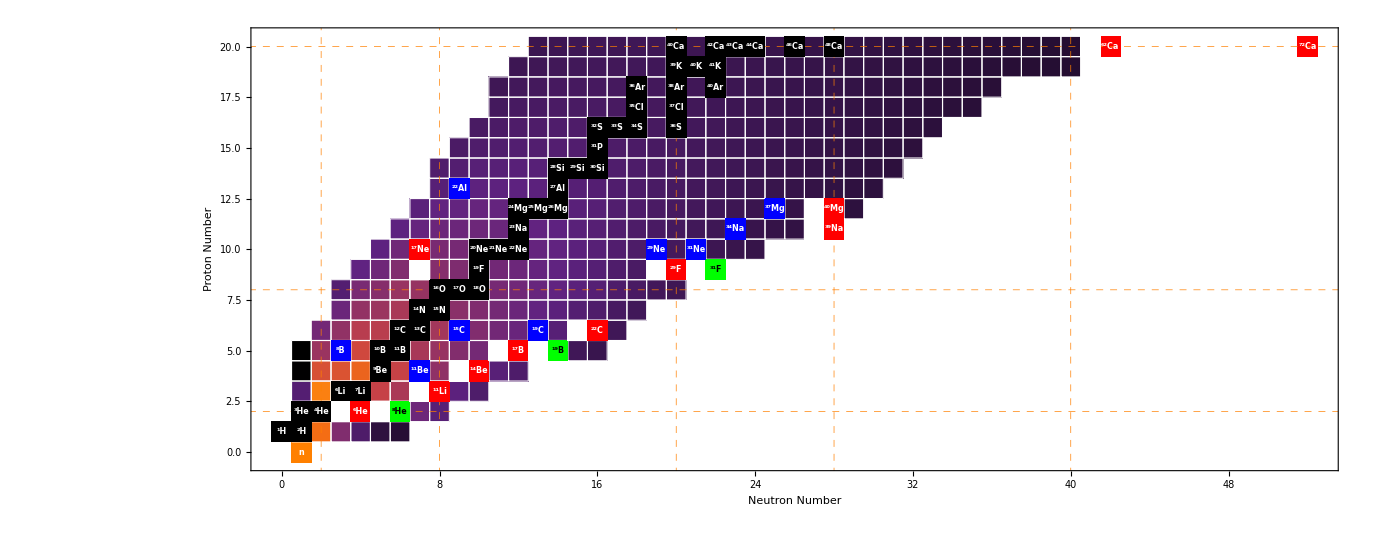

```mathematica
Graphics[{Block[{y=#[[1]],x=#[[2]]},{{color[#[[4]]/(#[[1]]+#[[2]])],EdgeForm[White],Rectangle[{x-1/2,y-1/2},{x+1/2,y+1/2}]}(*,Text[nucllab[#[[1]],#[[2]],##[[3]]],{x,y},BaseStyle->Large]*)}]&/@sel,
{Orange,Thick,Rectangle[{1-1/2,0-1/2},{1+1/2,0+1/2}]},
{White,Thick,Text[Style["n",FontSize->8,FontFamily->"Times", Bold],{1.0,0.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{0-1/2,1-1/2},{0+1/2,1+1/2}]},
{White,Thick,Text[Style["^1H",FontSize->8,FontFamily->"Times", Bold],{0.0,1.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{1-1/2,1-1/2},{1+1/2,1+1/2}]},
{White,Thick,Text[Style["^2H",FontSize->8,FontFamily->"Times", Bold],{1.0,1.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{1-1/2,2-1/2},{1+1/2,2+1/2}]},
{White,Thick,Text[Style["^3He",FontSize->8,FontFamily->"Times", Bold],{1.0,2.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{2-1/2,2-1/2},{2+1/2,2+1/2}]},
{White,Thick,Text[Style["^4He",FontSize->8,FontFamily->"Times", Bold],{2.0,2.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{3-1/2,3-1/2},{3+1/2,3+1/2}]},
{White,Thick,Text[Style["^6Li",FontSize->8,FontFamily->"Times", Bold],{3.0,3.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{4-1/2,3-1/2},{4+1/2,3+1/2}]},
{White,Thick,Text[Style["^7Li",FontSize->8,FontFamily->"Times", Bold],{4.0,3.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{5-1/2,4-1/2},{5+1/2,4+1/2}]},
{White,Thick,Text[Style["^9Be",FontSize->8,FontFamily->"Times", Bold],{5.0,4.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{5-1/2,5-1/2},{5+1/2,5+1/2}]},
{White,Thick,Text[Style["^10B",FontSize->8,FontFamily->"Times", Bold],{5.0,5.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{6-1/2,5-1/2},{6+1/2,5+1/2}]},
{White,Thick,Text[Style["^11B",FontSize->8,FontFamily->"Times", Bold],{6.0,5.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{6-1/2,6-1/2},{6+1/2,6+1/2}]},
{White,Thick,Text[Style["^12C",FontSize->8,FontFamily->"Times", Bold],{6.0,6.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{7-1/2,6-1/2},{7+1/2,6+1/2}]},
{White,Thick,Text[Style["^13C",FontSize->8,FontFamily->"Times", Bold],{7.0,6.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{7-1/2,7-1/2},{7+1/2,7+1/2}]},
{White,Thick,Text[Style["^14N",FontSize->8,FontFamily->"Times", Bold],{7.0,7.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{8-1/2,7-1/2},{8+1/2,7+1/2}]},
{White,Thick,Text[Style["^15N",FontSize->8,FontFamily->"Times", Bold],{8.0,7.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{8-1/2,8-1/2},{8+1/2,8+1/2}]},
{White,Thick,Text[Style["^16O",FontSize->8,FontFamily->"Times", Bold],{8.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{9-1/2,8-1/2},{9+1/2,8+1/2}]},
{White,Thick,Text[Style["^17O",FontSize->8,FontFamily->"Times", Bold],{9.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,8-1/2},{10+1/2,8+1/2}]},
{White,Thick,Text[Style["^18O",FontSize->8,FontFamily->"Times", Bold],{10.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,9-1/2},{10+1/2,9+1/2}]},
{White,Thick,Text[Style["^19F",FontSize->8,FontFamily->"Times", Bold],{10.0,9.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,10-1/2},{10+1/2,10+1/2}]},
{White,Thick,Text[Style["^20Ne",FontSize->8,FontFamily->"Times", Bold],{10.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{11-1/2,10-1/2},{11+1/2,10+1/2}]},
{White,Thick,Text[Style["^21Ne",FontSize->8,FontFamily->"Times", Bold],{11.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,10-1/2},{12+1/2,10+1/2}]},
{White,Thick,Text[Style["^22Ne",FontSize->8,FontFamily->"Times", Bold],{12.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,11-1/2},{12+1/2,11+1/2}]},
{White,Thick,Text[Style["^23Na",FontSize->8,FontFamily->"Times", Bold],{12.0,11.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,12-1/2},{12+1/2,12+1/2}]},
{White,Thick,Text[Style["^24Mg",FontSize->8,FontFamily->"Times", Bold],{12.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{13-1/2,12-1/2},{13+1/2,12+1/2}]},
{White,Thick,Text[Style["^25Mg",FontSize->8,FontFamily->"Times", Bold],{13.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,12-1/2},{14+1/2,12+1/2}]},
{White,Thick,Text[Style["^26Mg",FontSize->8,FontFamily->"Times", Bold],{14.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,13-1/2},{14+1/2,13+1/2}]},
{White,Thick,Text[Style["^27Al",FontSize->8,FontFamily->"Times", Bold],{14.0,13.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{9-1/2,13-1/2},{9+1/2,13+1/2}]},
{White,Thick,Text[Style["^22Al",FontSize->8,FontFamily->"Times", Bold],{9.0,13.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,14-1/2},{14+1/2,14+1/2}]},
{White,Thick,Text[Style["^28Si",FontSize->8,FontFamily->"Times", Bold],{14.0,14.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{15-1/2,14-1/2},{15+1/2,14+1/2}]},
{White,Thick,Text[Style["^29Si",FontSize->8,FontFamily->"Times", Bold],{15.0,14.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{16-1/2,14-1/2},{16+1/2,14+1/2}]},
{White,Thick,Text[Style["^30Si",FontSize->8,FontFamily->"Times", Bold],{16.0,14.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{16-1/2,15-1/2},{16+1/2,15+1/2}]},
{White,Thick,Text[Style["^31P",FontSize->8,FontFamily->"Times", Bold],{16.0,15.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{16-1/2,16-1/2},{16+1/2,16+1/2}]},
{White,Thick,Text[Style["^32S",FontSize->8,FontFamily->"Times", Bold],{16.0,16.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{17-1/2,16-1/2},{17+1/2,16+1/2}]},
{White,Thick,Text[Style["^33S",FontSize->8,FontFamily->"Times", Bold],{17.0,16.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{18-1/2,16-1/2},{18+1/2,16+1/2}]},
{White,Thick,Text[Style["^34S",FontSize->8,FontFamily->"Times", Bold],{18.0,16.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{20-1/2,16-1/2},{20+1/2,16+1/2}]},
{White,Thick,Text[Style["^36S",FontSize->8,FontFamily->"Times", Bold],{20.0,16.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{18-1/2,17-1/2},{18+1/2,17+1/2}]},
{White,Thick,Text[Style["^35Cl",FontSize->8,FontFamily->"Times", Bold],{18.0,17.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{20-1/2,17-1/2},{20+1/2,17+1/2}]},
{White,Thick,Text[Style["^37Cl",FontSize->8,FontFamily->"Times", Bold],{20.0,17.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{18-1/2,18-1/2},{18+1/2,18+1/2}]},
{White,Thick,Text[Style["^36Ar",FontSize->8,FontFamily->"Times", Bold],{18.0,18.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{20-1/2,18-1/2},{20+1/2,18+1/2}]},
{White,Thick,Text[Style["^38Ar",FontSize->8,FontFamily->"Times", Bold],{20.0,18.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{22-1/2,18-1/2},{22+1/2,18+1/2}]},
{White,Thick,Text[Style["^40Ar",FontSize->8,FontFamily->"Times", Bold],{22.0,18.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{20-1/2,19-1/2},{20+1/2,19+1/2}]},
{White,Thick,Text[Style["^39K",FontSize->8,FontFamily->"Times", Bold],{20.0,19.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{21-1/2,19-1/2},{21+1/2,19+1/2}]},
{White,Thick,Text[Style["^40K",FontSize->8,FontFamily->"Times", Bold],{21.0,19.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{22-1/2,19-1/2},{22+1/2,19+1/2}]},
{White,Thick,Text[Style["^41K",FontSize->8,FontFamily->"Times", Bold],{22.0,19.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{20-1/2,20-1/2},{20+1/2,20+1/2}]},
{White,Thick,Text[Style["^40Ca",FontSize->8,FontFamily->"Times", Bold],{20.0,20.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{22-1/2,20-1/2},{22+1/2,20+1/2}]},
{White,Thick,Text[Style["^42Ca",FontSize->8,FontFamily->"Times", Bold],{22.0,20.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{23-1/2,20-1/2},{23+1/2,20+1/2}]},
{White,Thick,Text[Style["^43Ca",FontSize->8,FontFamily->"Times", Bold],{23.0,20.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{24-1/2,20-1/2},{24+1/2,20+1/2}]},
{White,Thick,Text[Style["^44Ca",FontSize->8,FontFamily->"Times", Bold],{24.0,20.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{26-1/2,20-1/2},{26+1/2,20+1/2}]},
{White,Thick,Text[Style["^46Ca",FontSize->8,FontFamily->"Times", Bold],{26.0,20.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{28-1/2,20-1/2},{28+1/2,20+1/2}]},
{White,Thick,Text[Style["^48Ca",FontSize->8,FontFamily->"Times", Bold],{28.0,20.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{41-1/2,20-1/2},{41+1/2,20+1/2}]},
{Red,Thick,Rectangle[{42-1/2,20-1/2},{42+1/2,20+1/2}]},
{White,Thick,Text[Style["^62Ca",FontSize->8,FontFamily->"Times", Bold],{42.0,20.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{51-1/2,20-1/2},{51+1/2,20+1/2}]},
{Red,Thick,Rectangle[{52-1/2,20-1/2},{52+1/2,20+1/2}]},
{White,Thick,Text[Style["^72Ca",FontSize->8,FontFamily->"Times", Bold],{52.0,20.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{3-1/2,2-1/2},{3+1/2,2+1/2}]},
(*{Black,Thick,Text[Style["^5He",FontSize->8,FontFamily->"Times", Bold],{3.0,2.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{4-1/2,2-1/2},{4+1/2,2+1/2}]},
{White,Thick,Text[Style["^6He",FontSize->8,FontFamily->"Times", Bold],{4.0,2.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{5-1/2,2-1/2},{5+1/2,2+1/2}]},
(*{Black,Thick,Text[Style["^7He",FontSize->8,FontFamily->"Times", Bold],{5.0,2.0},Scaled[{.6,.6}]]},*)
{Green,Thick,Rectangle[{6-1/2,2-1/2},{6+1/2,2+1/2}]},
{Black,Thick,Text[Style["^8He",FontSize->8,FontFamily->"Times", Bold],{6.0,2.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{7-1/2,3-1/2},{7+1/2,3+1/2}]},
(*{Black,Thick,Text[Style["^10Li",FontSize->8,FontFamily->"Times", Bold],{7.0,3.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{8-1/2,3-1/2},{8+1/2,3+1/2}]},
{White,Thick,Text[Style["^11Li",FontSize->8,FontFamily->"Times", Bold],{8.0,3.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{7-1/2,4-1/2},{7+1/2,4+1/2}]},
{White,Thick,Text[Style["^11Be",FontSize->8,FontFamily->"Times", Bold],{7.0,4.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{9-1/2,4-1/2},{9+1/2,4+1/2}]},
(*{Black,Thick,Text[Style["^13Be",FontSize->8,FontFamily->"Times", Bold],{9.0,4.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{10-1/2,4-1/2},{10+1/2,4+1/2}]},
{White,Thick,Text[Style["^14Be",FontSize->8,FontFamily->"Times", Bold],{10.0,4.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{3-1/2,5-1/2},{3+1/2,5+1/2}]},
{White,Thick,Text[Style["^8B",FontSize->8,FontFamily->"Times", Bold],{3.0,5.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{11-1/2,5-1/2},{11+1/2,5+1/2}]},
(*{Black,Thick,Text[Style["^16B",FontSize->8,FontFamily->"Times", Bold],{11.0,5.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{12-1/2,5-1/2},{12+1/2,5+1/2}]},
{White,Thick,Text[Style["^17B",FontSize->8,FontFamily->"Times", Bold],{12.0,5.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{13-1/2,5-1/2},{13+1/2,5+1/2}]},
(*{Black,Thick,Text[Style["^18B",FontSize->8,FontFamily->"Times", Bold],{13.0,5.0},Scaled[{.6,.6}]]},*)
{Green,Thick,Rectangle[{14-1/2,5-1/2},{14+1/2,5+1/2}]},
{Black,Thick,Text[Style["^19B",FontSize->8,FontFamily->"Times", Bold],{14.0,5.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{9-1/2,6-1/2},{9+1/2,6+1/2}]},
{White,Thick,Text[Style["^15C",FontSize->8,FontFamily->"Times", Bold],{9.0,6.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{13-1/2,6-1/2},{13+1/2,6+1/2}]},
{White,Thick,Text[Style["^19C",FontSize->8,FontFamily->"Times", Bold],{13.0,6.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{15-1/2,6-1/2},{15+1/2,6+1/2}]},
{Red,Thick,Rectangle[{16-1/2,6-1/2},{16+1/2,6+1/2}]},
{White,Thick,Text[Style["^22C",FontSize->8,FontFamily->"Times", Bold],{16.0,6.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{19-1/2,9-1/2},{19+1/2,9+1/2}]},
{Red,Thick,Rectangle[{20-1/2,9-1/2},{20+1/2,9+1/2}]},
{White,Thick,Text[Style["^29F",FontSize->8,FontFamily->"Times", Bold],{20.0,9.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{21-1/2,9-1/2},{21+1/2,9+1/2}]},
{Green,Thick,Rectangle[{22-1/2,9-1/2},{22+1/2,9+1/2}]},
{Black,Thick,Text[Style["^31F",FontSize->8,FontFamily->"Times", Bold],{22.0,9.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{19-1/2,10-1/2},{19+1/2,10+1/2}]},
{White,Thick,Text[Style["^29Ne",FontSize->8,FontFamily->"Times", Bold],{19.0,10.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{21-1/2,10-1/2},{21+1/2,10+1/2}]},
{White,Thick,Text[Style["^31Ne",FontSize->8,FontFamily->"Times", Bold],{21.0,10.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{23-1/2,11-1/2},{23+1/2,11+1/2}]},
{White,Thick,Text[Style["^34Na",FontSize->8,FontFamily->"Times", Bold],{23.0,11.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{25-1/2,12-1/2},{25+1/2,12+1/2}]},
{White,Thick,Text[Style["^37Mg",FontSize->8,FontFamily->"Times", Bold],{25.0,12.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{27-1/2,11-1/2},{27+1/2,11+1/2}]},
{Red,Thick,Rectangle[{28-1/2,11-1/2},{28+1/2,11+1/2}]},
{White,Thick,Text[Style["^39Na",FontSize->8,FontFamily->"Times", Bold],{28.0,11.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{27-1/2,12-1/2},{27+1/2,12+1/2}]},
{Red,Thick,Rectangle[{28-1/2,12-1/2},{28+1/2,12+1/2}]},
{White,Thick,Text[Style["^40Mg",FontSize->8,FontFamily->"Times", Bold],{28.0,12.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{7-1/2,9-1/2},{7+1/2,9+1/2}]},
{Red,Thick,Rectangle[{7-1/2,10-1/2},{7+1/2,10+1/2}]},{White,Thick,Text[Style["^17Ne",FontSize->8,FontFamily->"Times", Bold],{7.0,10.0},Scaled[{.6,.6}]]}
},Frame->True,FrameTicksStyle->Directive[Black,Large],FrameLabel->{"Neutron Number", "Proton Number"},LabelStyle->Directive[Large,Black],GridLines->{{2,8,20,28,40},{2,8,20,28,40}},GridLinesStyle->Directive[Orange,Thick,Dashed]]
```

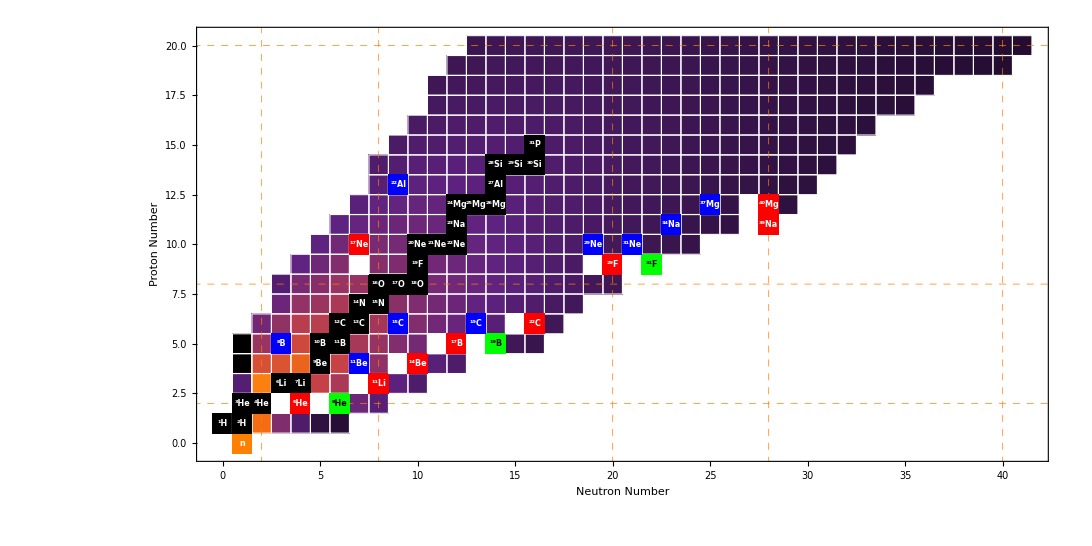

```mathematica
Graphics[{Block[{y=#[[1]],x=#[[2]]},{{color[#[[4]]/(#[[1]]+#[[2]])],EdgeForm[White],Rectangle[{x-1/2,y-1/2},{x+1/2,y+1/2}]}(*,Text[nucllab[#[[1]],#[[2]],##[[3]]],{x,y},BaseStyle->Large]*)}]&/@sel,
{Orange,Thick,Rectangle[{1-1/2,0-1/2},{1+1/2,0+1/2}]},
{White,Thick,Text[Style["n",FontSize->8,FontFamily->"Times", Bold],{1.0,0.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{0-1/2,1-1/2},{0+1/2,1+1/2}]},
{White,Thick,Text[Style["^1H",FontSize->8,FontFamily->"Times", Bold],{0.0,1.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{1-1/2,1-1/2},{1+1/2,1+1/2}]},
{White,Thick,Text[Style["^2H",FontSize->8,FontFamily->"Times", Bold],{1.0,1.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{1-1/2,2-1/2},{1+1/2,2+1/2}]},
{White,Thick,Text[Style["^3He",FontSize->8,FontFamily->"Times", Bold],{1.0,2.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{2-1/2,2-1/2},{2+1/2,2+1/2}]},
{White,Thick,Text[Style["^4He",FontSize->8,FontFamily->"Times", Bold],{2.0,2.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{3-1/2,3-1/2},{3+1/2,3+1/2}]},
{White,Thick,Text[Style["^6Li",FontSize->8,FontFamily->"Times", Bold],{3.0,3.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{4-1/2,3-1/2},{4+1/2,3+1/2}]},
{White,Thick,Text[Style["^7Li",FontSize->8,FontFamily->"Times", Bold],{4.0,3.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{5-1/2,4-1/2},{5+1/2,4+1/2}]},
{White,Thick,Text[Style["^9Be",FontSize->8,FontFamily->"Times", Bold],{5.0,4.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{5-1/2,5-1/2},{5+1/2,5+1/2}]},
{White,Thick,Text[Style["^10B",FontSize->8,FontFamily->"Times", Bold],{5.0,5.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{6-1/2,5-1/2},{6+1/2,5+1/2}]},
{White,Thick,Text[Style["^11B",FontSize->8,FontFamily->"Times", Bold],{6.0,5.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{6-1/2,6-1/2},{6+1/2,6+1/2}]},
{White,Thick,Text[Style["^12C",FontSize->8,FontFamily->"Times", Bold],{6.0,6.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{7-1/2,6-1/2},{7+1/2,6+1/2}]},
{White,Thick,Text[Style["^13C",FontSize->8,FontFamily->"Times", Bold],{7.0,6.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{7-1/2,7-1/2},{7+1/2,7+1/2}]},
{White,Thick,Text[Style["^14N",FontSize->8,FontFamily->"Times", Bold],{7.0,7.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{8-1/2,7-1/2},{8+1/2,7+1/2}]},
{White,Thick,Text[Style["^15N",FontSize->8,FontFamily->"Times", Bold],{8.0,7.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{8-1/2,8-1/2},{8+1/2,8+1/2}]},
{White,Thick,Text[Style["^16O",FontSize->8,FontFamily->"Times", Bold],{8.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{9-1/2,8-1/2},{9+1/2,8+1/2}]},
{White,Thick,Text[Style["^17O",FontSize->8,FontFamily->"Times", Bold],{9.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,8-1/2},{10+1/2,8+1/2}]},
{White,Thick,Text[Style["^18O",FontSize->8,FontFamily->"Times", Bold],{10.0,8.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,9-1/2},{10+1/2,9+1/2}]},
{White,Thick,Text[Style["^19F",FontSize->8,FontFamily->"Times", Bold],{10.0,9.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{10-1/2,10-1/2},{10+1/2,10+1/2}]},
{White,Thick,Text[Style["^20Ne",FontSize->8,FontFamily->"Times", Bold],{10.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{11-1/2,10-1/2},{11+1/2,10+1/2}]},
{White,Thick,Text[Style["^21Ne",FontSize->8,FontFamily->"Times", Bold],{11.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,10-1/2},{12+1/2,10+1/2}]},
{White,Thick,Text[Style["^22Ne",FontSize->8,FontFamily->"Times", Bold],{12.0,10.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,11-1/2},{12+1/2,11+1/2}]},
{White,Thick,Text[Style["^23Na",FontSize->8,FontFamily->"Times", Bold],{12.0,11.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{12-1/2,12-1/2},{12+1/2,12+1/2}]},
{White,Thick,Text[Style["^24Mg",FontSize->8,FontFamily->"Times", Bold],{12.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{13-1/2,12-1/2},{13+1/2,12+1/2}]},
{White,Thick,Text[Style["^25Mg",FontSize->8,FontFamily->"Times", Bold],{13.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,12-1/2},{14+1/2,12+1/2}]},
{White,Thick,Text[Style["^26Mg",FontSize->8,FontFamily->"Times", Bold],{14.0,12.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,13-1/2},{14+1/2,13+1/2}]},
{White,Thick,Text[Style["^27Al",FontSize->8,FontFamily->"Times", Bold],{14.0,13.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{9-1/2,13-1/2},{9+1/2,13+1/2}]},
{White,Thick,Text[Style["^22Al",FontSize->8,FontFamily->"Times", Bold],{9.0,13.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{14-1/2,14-1/2},{14+1/2,14+1/2}]},
{White,Thick,Text[Style["^28Si",FontSize->8,FontFamily->"Times", Bold],{14.0,14.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{15-1/2,14-1/2},{15+1/2,14+1/2}]},
{White,Thick,Text[Style["^29Si",FontSize->8,FontFamily->"Times", Bold],{15.0,14.0},Scaled[{.6,.6}]]},
{Black,Thick,Rectangle[{16-1/2,14-1/2},{16+1/2,14+1/2}]},
{White,Thick,Text[Style["^30Si",FontSize->8,FontFamily->"Times", Bold],{16.0,14.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{3-1/2,2-1/2},{3+1/2,2+1/2}]},
{Black,Thick,Rectangle[{16-1/2,15-1/2},{16+1/2,15+1/2}]},
{White,Thick,Text[Style["^31P",FontSize->8,FontFamily->"Times", Bold],{16.0,15.0},Scaled[{.6,.6}]]},
(*{Black,Thick,Text[Style["^5He",FontSize->8,FontFamily->"Times", Bold],{3.0,2.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{4-1/2,2-1/2},{4+1/2,2+1/2}]},
{White,Thick,Text[Style["^6He",FontSize->8,FontFamily->"Times", Bold],{4.0,2.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{5-1/2,2-1/2},{5+1/2,2+1/2}]},
(*{Black,Thick,Text[Style["^7He",FontSize->8,FontFamily->"Times", Bold],{5.0,2.0},Scaled[{.6,.6}]]},*)
{Green,Thick,Rectangle[{6-1/2,2-1/2},{6+1/2,2+1/2}]},
{Black,Thick,Text[Style["^8He",FontSize->8,FontFamily->"Times", Bold],{6.0,2.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{7-1/2,3-1/2},{7+1/2,3+1/2}]},
(*{Black,Thick,Text[Style["^10Li",FontSize->8,FontFamily->"Times", Bold],{7.0,3.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{8-1/2,3-1/2},{8+1/2,3+1/2}]},
{White,Thick,Text[Style["^11Li",FontSize->8,FontFamily->"Times", Bold],{8.0,3.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{7-1/2,4-1/2},{7+1/2,4+1/2}]},
{White,Thick,Text[Style["^11Be",FontSize->8,FontFamily->"Times", Bold],{7.0,4.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{9-1/2,4-1/2},{9+1/2,4+1/2}]},
(*{Black,Thick,Text[Style["^13Be",FontSize->8,FontFamily->"Times", Bold],{9.0,4.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{10-1/2,4-1/2},{10+1/2,4+1/2}]},
{White,Thick,Text[Style["^14Be",FontSize->8,FontFamily->"Times", Bold],{10.0,4.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{3-1/2,5-1/2},{3+1/2,5+1/2}]},
{White,Thick,Text[Style["^8B",FontSize->8,FontFamily->"Times", Bold],{3.0,5.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{11-1/2,5-1/2},{11+1/2,5+1/2}]},
(*{Black,Thick,Text[Style["^16B",FontSize->8,FontFamily->"Times", Bold],{11.0,5.0},Scaled[{.6,.6}]]},*)
{Red,Thick,Rectangle[{12-1/2,5-1/2},{12+1/2,5+1/2}]},
{White,Thick,Text[Style["^17B",FontSize->8,FontFamily->"Times", Bold],{12.0,5.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{13-1/2,5-1/2},{13+1/2,5+1/2}]},
(*{Black,Thick,Text[Style["^18B",FontSize->8,FontFamily->"Times", Bold],{13.0,5.0},Scaled[{.6,.6}]]},*)
{Green,Thick,Rectangle[{14-1/2,5-1/2},{14+1/2,5+1/2}]},
{Black,Thick,Text[Style["^19B",FontSize->8,FontFamily->"Times", Bold],{14.0,5.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{9-1/2,6-1/2},{9+1/2,6+1/2}]},
{White,Thick,Text[Style["^15C",FontSize->8,FontFamily->"Times", Bold],{9.0,6.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{13-1/2,6-1/2},{13+1/2,6+1/2}]},
{White,Thick,Text[Style["^19C",FontSize->8,FontFamily->"Times", Bold],{13.0,6.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{15-1/2,6-1/2},{15+1/2,6+1/2}]},
{Red,Thick,Rectangle[{16-1/2,6-1/2},{16+1/2,6+1/2}]},
{White,Thick,Text[Style["^22C",FontSize->8,FontFamily->"Times", Bold],{16.0,6.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{19-1/2,9-1/2},{19+1/2,9+1/2}]},
{Red,Thick,Rectangle[{20-1/2,9-1/2},{20+1/2,9+1/2}]},
{White,Thick,Text[Style["^29F",FontSize->8,FontFamily->"Times", Bold],{20.0,9.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{21-1/2,9-1/2},{21+1/2,9+1/2}]},
{Green,Thick,Rectangle[{22-1/2,9-1/2},{22+1/2,9+1/2}]},
{Black,Thick,Text[Style["^31F",FontSize->8,FontFamily->"Times", Bold],{22.0,9.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{19-1/2,10-1/2},{19+1/2,10+1/2}]},
{White,Thick,Text[Style["^29Ne",FontSize->8,FontFamily->"Times", Bold],{19.0,10.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{21-1/2,10-1/2},{21+1/2,10+1/2}]},
{White,Thick,Text[Style["^31Ne",FontSize->8,FontFamily->"Times", Bold],{21.0,10.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{23-1/2,11-1/2},{23+1/2,11+1/2}]},
{White,Thick,Text[Style["^34Na",FontSize->8,FontFamily->"Times", Bold],{23.0,11.0},Scaled[{.6,.6}]]},
{Blue,Thick,Rectangle[{25-1/2,12-1/2},{25+1/2,12+1/2}]},
{White,Thick,Text[Style["^37Mg",FontSize->8,FontFamily->"Times", Bold],{25.0,12.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{27-1/2,11-1/2},{27+1/2,11+1/2}]},
{Red,Thick,Rectangle[{28-1/2,11-1/2},{28+1/2,11+1/2}]},
{White,Thick,Text[Style["^39Na",FontSize->8,FontFamily->"Times", Bold],{28.0,11.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{27-1/2,12-1/2},{27+1/2,12+1/2}]},
{Red,Thick,Rectangle[{28-1/2,12-1/2},{28+1/2,12+1/2}]},
{White,Thick,Text[Style["^40Mg",FontSize->8,FontFamily->"Times", Bold],{28.0,12.0},Scaled[{.6,.6}]]},
{White,Thick,Rectangle[{7-1/2,9-1/2},{7+1/2,9+1/2}]},
{Red,Thick,Rectangle[{7-1/2,10-1/2},{7+1/2,10+1/2}]},{White,Thick,Text[Style["^17Ne",FontSize->8,FontFamily->"Times", Bold],{7.0,10.0},Scaled[{.6,.6}]]}
},Frame->True,FrameTicksStyle->Directive[Black,Large],FrameLabel->{"Neutron Number", "Proton Number"},LabelStyle->Directive[Large,Black],GridLines->{{2,8,20,28,40},{2,8,20,28,40}},GridLinesStyle->Directive[Orange,Thick,Dashed]]
```

```mathematica
Export["/home_th/singh/OneDrive/Review_IITR/Intro figure/2.eps",%188,"EPS"]
```

/home_th/singh/OneDrive/Review_IITR/Intro figure/2.eps

```mathematica
Export["/home_th/singh/OneDrive/Review_IITR/Intro figure/1.eps",%169,"EPS"]
```

/home_th/singh/OneDrive/Review_IITR/Intro figure/1.eps